```mathematica
$HistoryLength=0;
SetDirectory[NotebookDirectory[]];
```

-Graphics-

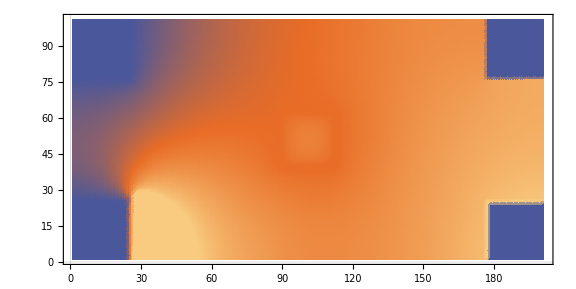

```mathematica
data = Import["cmake-build-release/temp2.txt","Table"];
ListContourPlot[Reverse@data,PlotTheme->"Scientific",PlotRange->{Full,Full,{100,200}},AspectRatio->Length[#]/Length[#[[1]]]&@data,PlotLegends->Automatic,Contours->30,ImageSize->Large,ClippingStyle->Automatic]
ListDensityPlot[Reverse@data,PlotTheme->"Scientific",PlotRange->{Full,Full,{100,200}},AspectRatio->Length[#]/Length[#[[1]]]&@data,PlotLegends->Automatic,ImageSize->Large,ClippingStyle->Automatic]
```

```mathematica
datas = Import[#,"Table"]&/@FileNames["cmake-build-release/r/*_r"]
```

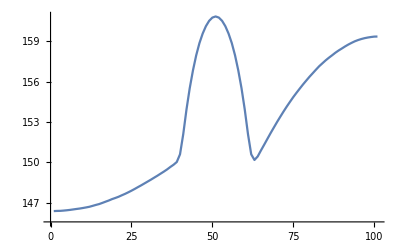

```mathematica
ListLinePlot[data[[;;,100]],PlotRange->Full]
```

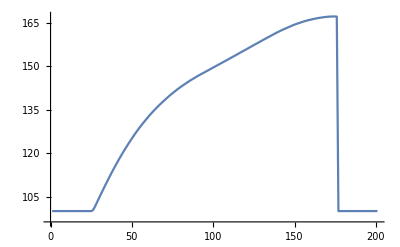

```mathematica
ListLinePlot[data[[10]],PlotRange->Full]
```